# Growth Function for ΛCDM k = 0,Ω_m+Ω_Λ=1

```mathematica
H[a_]:=Subscript[H, 0](Subscript[Ω, m] a^-3+Subscript[Ω, Λ])^(1/2)
```

```mathematica
Integrate[(a*Subscript[Ω, m0])/((Subscript[Ω, m0]/(a*x)+Subscript[Ω, Λ0](a*x)^2)^(3./2)),{x,0,1},Assumptions:>0<Subscript[Ω, m0]<1&&0<Subscript[Ω, Λ0]<1&&0<a<1]
```

```mathematica
SuperPlus[D][a_]:=(H[a]/Subscript[H, 0])*(a^2.5 Hypergeometric2F1[0.8333333333333335,1.5,1.8333333333333335,-(a^3 Subscript[Ω, Λ0])/Subscript[Ω, m0]])/Subscript[Ω, m0]^0.5
```

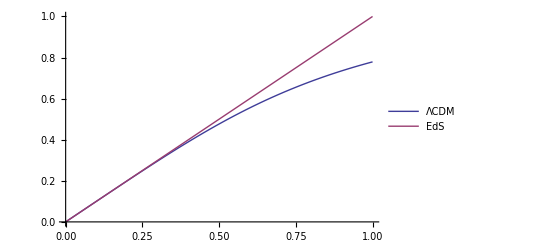

```mathematica
Subscript[Ω, m0]=0.3;
Subscript[Ω, Λ0]=0.7;
Plot[{SuperPlus[D][x],x},{x,0,1},PlotLegends->{"ΛCDM","EdS"}]
```

```mathematica
`
```